```mathematica
v=9;
ig[v][5]=Interpolation[gap5v9];
ig[v][10]=Interpolation[gap10v9];
ig[v][20]=Interpolation[gap20v9];
ig[v][30]=Interpolation[gap30v9];
ig[v][40]=Interpolation[gap40v9];
ig[v][50]=Interpolation[gap50v9];
```

```mathematica
v=9;
g[v][5]= gap5v9;
g[v][10]= gap10v9;
g[v][20]= gap20v9;
g[v][30]= gap30v9;
g[v][40]= gap40v9;
g[v][50]= gap50v9;
```

```mathematica
g[9][10];
```

```mathematica
δ=0.00075;
Do[

g[v][l]=Table[{g[v][l][[All,1]][[i]],g[v][l][[All,2]][[i]]},{i,1,Length[g[v][l]]}];
g1[v][l]=Table[{g[v][l][[All,1]][[i]],g[v][l][[All,2]][[i]]},{i,1,Length[g[v][l]],2}];
g2[v][l]=Table[{g[v][l][[All,1]][[i]],g[v][l][[All,2]][[i]]},{i,2,Length[g[v][l]],2}];

ig[v][l]=Interpolation[g[v][l]];
ig1[v][l]=Interpolation[g1[v][l]];
ig2[v][l]=Interpolation[g2[v][l]];

dgdd[v][l]=Table[{x,(ig[v][l][x+δ]-ig[v][l][x-δ])/(2*δ)},{x,0.0815,0.087,0.0001}];
dg1dd[v][l]=Table[{x,(ig1[v][l][x+δ]-ig1[v][l][x-δ])/(2*δ)},{x,0.0815,0.087,0.0001}];
dg2dd[v][l]=Table[{x,(ig2[v][l][x+δ]-ig2[v][l][x-δ])/(2*δ)},{x,0.0815,0.087,0.0001}];

(*dgdd[v][l]=Table[{g[v][l][[All,1]][[i]],(g[v][l][[All,2]][[i+2]]-g[v][l][[All,2]][[i-2]])/(g[v][l][[All,1]][[i+2]]-g[v][l][[All,1]][[i-2]])},{i,3,Length[g[v][l]]-2}];

dg1dd[v][l]=Table[{g1[v][l][[All,1]][[i]],(g1[v][l][[All,2]][[i+1]]-g1[v][l][[All,2]][[i-1]])/(g1[v][l][[All,1]][[i+1]]-g1[v][l][[All,1]][[i-1]])},{i,2,Length[g1[v][l]]-1}];

dg2dd[v][l]=Table[{g2[v][l][[All,1]][[i]],(g2[v][l][[All,2]][[i+1]]-g2[v][l][[All,2]][[i-1]])/(g2[v][l][[All,1]][[i+1]]-g2[v][l][[All,1]][[i-1]])},{i,2,Length[g2[v][l]]-1}];*)

,{l,{5,10,20,30,40,50}}]
```

```mathematica
dgdd[v][l];
dg1dd[v][l];
dg2dd[v][l];
```

20

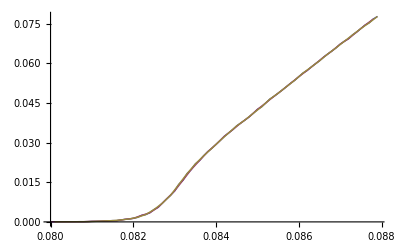

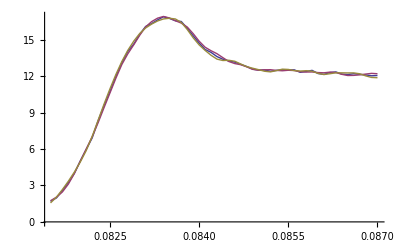

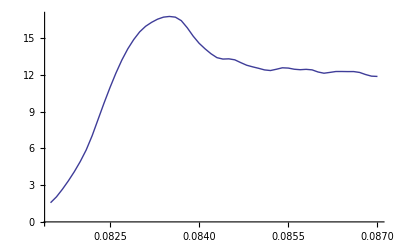

```mathematica
l=20
ListLinePlot[{g[v][l],g1[v][l],g2[v][l]}]
ListLinePlot[{dgdd[v][l],dg1dd[v][l],dg2dd[v][l]}]
ListLinePlot[{dg2dd[v][l]}]
```

```mathematica
maxdgdd[v]=Table[{l*1000,Max[dgdd[v][l][[All,2]]]},{l,{5,10,20,30,50}}]

Logmaxdgdd[v]=Table[{Log[maxdgdd[v][[All,1]][[i]]],Log[maxdgdd[v][[All,2]][[i]]]},{i,1,Length[maxdgdd[v]]}]

pmaxdgdd[v]=Table[{maxdgdd[v][[All,1]][[i]],Select[dgdd[v][maxdgdd[v][[All,1]][[i]]/1000],#[[2]]==maxdgdd[v][[All,2]][[i]]&][[All,1]][[1]]},{i,1,Length[maxdgdd[v]]}]

vvpmaxdgdd[v]=Table[{pmaxdgdd[v][[All,1]][[i]],ig[v][pmaxdgdd[v][[All,1]][[i]]/1000][pmaxdgdd[v][[All,2]][[i]]]},{i,1,Length[pmaxdgdd[v]]}]


Logvvpmaxdgdd[v]=Table[{Log[vvpmaxdgdd[v][[All,1]][[i]]],Log[vvpmaxdgdd[v][[All,2]][[i]]]},{i,1,Length[vvpmaxdgdd[v]]}]



maxdg1dd[v]=Table[{l*1000,Max[dg1dd[v][l][[All,2]]]},{l,{5,10,20,30,50}}]

Logmaxdg1dd[v]=Table[{Log[maxdg1dd[v][[All,1]][[i]]],Log[maxdg1dd[v][[All,2]][[i]]]},{i,1,Length[maxdg1dd[v]]}]

pmaxdg1dd[v]=Table[{maxdg1dd[v][[All,1]][[i]],Select[dg1dd[v][maxdg1dd[v][[All,1]][[i]]/1000],#[[2]]==maxdg1dd[v][[All,2]][[i]]&][[All,1]][[1]]},{i,1,Length[maxdg1dd[v]]}]

vvpmaxdg1dd[v]=Table[{pmaxdg1dd[v][[All,1]][[i]],ig1[v][pmaxdg1dd[v][[All,1]][[i]]/1000][pmaxdg1dd[v][[All,2]][[i]]]},{i,1,Length[pmaxdg1dd[v]]}]


Logvvpmaxdg1dd[v]=Table[{Log[vvpmaxdg1dd[v][[All,1]][[i]]],Log[vvpmaxdg1dd[v][[All,2]][[i]]]},{i,1,Length[vvpmaxdg1dd[v]]}]

maxdg2dd[v]=Table[{l*1000,Max[dg2dd[v][l][[All,2]]]},{l,{5,10,20,30,50}}]

Logmaxdg2dd[v]=Table[{Log[maxdg2dd[v][[All,1]][[i]]],Log[maxdg2dd[v][[All,2]][[i]]]},{i,1,Length[maxdg2dd[v]]}]

pmaxdg2dd[v]=Table[{maxdg2dd[v][[All,1]][[i]],Select[dg2dd[v][maxdg2dd[v][[All,1]][[i]]/1000],#[[2]]==maxdg2dd[v][[All,2]][[i]]&][[All,1]][[1]]},{i,1,Length[maxdg2dd[v]]}]

vvpmaxdg2dd[v]=Table[{pmaxdg2dd[v][[All,1]][[i]],ig2[v][pmaxdg2dd[v][[All,1]][[i]]/1000][pmaxdg2dd[v][[All,2]][[i]]]},{i,1,Length[pmaxdg2dd[v]]}]


Logvvpmaxdg2dd[v]=Table[{Log[vvpmaxdg2dd[v][[All,1]][[i]]],Log[vvpmaxdg2dd[v][[All,2]][[i]]]},{i,1,Length[vvpmaxdg2dd[v]]}]
```

{{5000,24.9136},{10000,20.3901},{20000,16.9083},{30000,15.0917},{50000,13.577}}

{{Log[5000],3.21541},{Log[10000],3.01505},{Log[20000],2.8278},{Log[30000],2.71415},{Log[50000],2.60838}}

{{5000,0.0854},{10000,0.084},{20000,0.0834},{30000,0.083},{50000,0.0828}}

{{5000,0.0340395},{10000,0.0201252},{20000,0.0197912},{30000,0.0161758},{50000,0.0152057}}

{{Log[5000],-3.38023},{Log[10000],-3.90578},{Log[20000],-3.92252},{Log[30000],-4.12424},{Log[50000],-4.18609}}

{{5000,24.3672},{10000,20.1298},{20000,16.9327},{30000,14.9791},{50000,13.3911}}

{{Log[5000],3.19324},{Log[10000],3.0022},{Log[20000],2.82925},{Log[30000],2.70666},{Log[50000],2.59459}}

{{5000,0.0853},{10000,0.0842},{20000,0.0834},{30000,0.083},{50000,0.0831}}

{{5000,0.0316654},{10000,0.026253},{20000,0.0197912},{30000,0.0161758},{50000,0.0195565}}

{{Log[5000],-3.45253},{Log[10000],-3.63998},{Log[20000],-3.92252},{Log[30000],-4.12424},{Log[50000],-3.93445}}

{{5000,25.1396},{10000,20.6371},{20000,16.7831},{30000,15.1468},{50000,13.7771}}

{{Log[5000],3.22444},{Log[10000],3.02709},{Log[20000],2.82037},{Log[30000],2.71779},{Log[50000],2.62301}}

{{5000,0.0853},{10000,0.084},{20000,0.0835},{30000,0.083},{50000,0.0829}}

{{5000,0.0313318},{10000,0.020979},{20000,0.0219276},{30000,0.0161072},{50000,0.0167205}}

{{Log[5000],-3.46312},{Log[10000],-3.86423},{Log[20000],-3.82001},{Log[30000],-4.12849},{Log[50000],-4.09112}}

```mathematica
Logmaxdg1dd[v]
Logvvpmaxdg1dd[v]
pmaxdg1dd[v]
```

{{Log[5000],3.19324},{Log[10000],3.0022},{Log[20000],2.82925},{Log[30000],2.70666},{Log[50000],2.59459}}

{{Log[5000],-3.45253},{Log[10000],-3.63998},{Log[20000],-3.92252},{Log[30000],-4.12424},{Log[50000],-3.93445}}

{{5000,0.0853},{10000,0.0842},{20000,0.0834},{30000,0.083},{50000,0.0831}}

```mathematica
k0=0.08122;
ClearAll[a0,b0,d0,ex0,c0]
model1=a0*x-b0;
model2=k0+c0*x^(-ex0)

nlfg1=NonlinearModelFit[Logvvpmaxdgdd[v],model1,{a0,b0},x];
nlfg1[{"BestFit","ParameterTable"}]

nlfg11=NonlinearModelFit[Logvvpmaxdg1dd[v],model1,{a0,b0},x];
nlfg11[{"BestFit","ParameterTable"}]

nlfg21=NonlinearModelFit[Logvvpmaxdg2dd[v],model1,{a0,b0},x];
nlfg21[{"BestFit","ParameterTable"}]

nlfg2=NonlinearModelFit[pmaxdgdd[v],model2,{c0,ex0},x];
nlfg2[{"BestFit","ParameterTable"}]

nlfg12=NonlinearModelFit[pmaxdg1dd[v],model2,{c0,ex0},x];
nlfg12[{"BestFit","ParameterTable"}]

nlfg22=NonlinearModelFit[pmaxdg2dd[v],model2,{c0,ex0},x];
nlfg22[{"BestFit","ParameterTable"}]
```

0.08122+c0 x^-ex0

{-0.726264-0.325833 x, | Estimate | Standard Error | t-Statistic | P-Value
a0 | -0.325833 | 0.0734789 | -4.43437 | 0.0213144
b0 | 0.726264 | 0.719038 | 1.01005 | 0.386868}

{-1.27132-0.260812 x, | Estimate | Standard Error | t-Statistic | P-Value
a0 | -0.260812 | 0.0776787 | -3.35757 | 0.0438121
b0 | 1.27132 | 0.760136 | 1.67249 | 0.193022}

{-1.27191-0.266766 x, | Estimate | Standard Error | t-Statistic | P-Value
a0 | -0.266766 | 0.070805 | -3.76761 | 0.0327192
b0 | 1.27191 | 0.692873 | 1.8357 | 0.163737}

{0.08122+0.194499/x^0.453773, | Estimate | Standard Error | t-Statistic | P-Value
c0 | 0.194499 | 0.0625749 | 3.10825 | 0.0529535
ex0 | 0.453773 | 0.0349612 | 12.9793 | 0.000987445}

{0.08122+0.123151/x^0.402153, | Estimate | Standard Error | t-Statistic | P-Value
c0 | 0.123151 | 0.0524666 | 2.34723 | 0.100558
ex0 | 0.402153 | 0.0459979 | 8.74284 | 0.00315085}

{0.08122+0.141019/x^0.418901, | Estimate | Standard Error | t-Statistic | P-Value
c0 | 0.141019 | 0.0496628 | 2.83953 | 0.0656718
ex0 | 0.418901 | 0.0381041 | 10.9936 | 0.00161163}

```mathematica
a=nlfg1["ParameterTableEntries"][[1]][[1]]
a1=nlfg11["ParameterTableEntries"][[1]][[1]];
a2=nlfg21["ParameterTableEntries"][[1]][[1]];

c=nlfg2["ParameterTableEntries"][[1]][[1]]
c1=nlfg12["ParameterTableEntries"][[1]][[1]];
c2=nlfg22["ParameterTableEntries"][[1]][[1]];

ex=-nlfg2["ParameterTableEntries"][[2]][[1]]
ex1=-nlfg12["ParameterTableEntries"][[2]][[1]];
ex2=-nlfg22["ParameterTableEntries"][[2]][[1]];
```

-0.325833

0.194499

-0.453773

```mathematica
l1=5;
l2=10;
l3=20;
l4=50;
l5=30;
Do[

input[l]=Table[{(g[v][l][[All,1]][[i]]-(k0+c*(l*1000)^(ex))),g[v][l][[All,2]][[i]]*(l*1000)^(-a)},{i,1,Length[g[v][l]]}];
input1[l]=Table[{(g1[v][l][[All,1]][[i]]-(k0+c1*(l*1000)^(ex1))),g1[v][l][[All,2]][[i]]*(l*1000)^(-a1)},{i,1,Length[g1[v][l]]}];
input2[l]=Table[{(g2[v][l][[All,1]][[i]]-(k0+c2*(l*1000)^(ex2))),g2[v][l][[All,2]][[i]]*(l*1000)^(-a2)},{i,1,Length[g2[v][l]]}];
,{l,{l1,l2,l3,l4,l5}}]
```

```mathematica
aux=1000;

For[z=0,z<0.4,z+=0.01,


Do[
dat[l]=Table[{(input[l][[All,1]][[i]])*(l*1000)^z,input[l][[All,2]][[i]]},{i,1,Length[input[l]]}];
in[l]=Interpolation[dat[l]]
,{l,{l1,l2,l3,l4}}];


min=Max[dat[l1][[All,1]][[1]],dat[l2][[All,1]][[1]],dat[l3][[All,1]][[1]],dat[l4][[All,1]][[1]]];
max=Min[dat[l1][[All,1]][[Length[dat[l1]]]],dat[l2][[All,1]][[Length[dat[l2]]]],dat[l3][[All,1]][[Length[dat[l3]]]],dat[l4][[All,1]][[Length[dat[l4]]]]];

val=NIntegrate[Abs[Log[Max[in[l1][x],in[l2][x],in[l3][x],in[l4][x]]]-Log[Min[in[l1][x],in[l2][x],in[l3][x],in[l4][x]]]],{x,min,max}]/((max-min)*(Log[Max[in[l1][max],in[l2][max],in[l3][max],in[l4][max]]]-Log[Min[in[l1][min],in[l2][min],in[l3][min],in[l4][min]]]));
(*Print[val]*)
(*sum=Append[sum,{z,val}];*)

If[val<aux,
aux=val;
zf=z;

]
]

aux
"= zf"zf
```

0.019928

0.17 = zf

```mathematica
aux=1000;

For[z=0,z<0.4,z+=0.01,


Do[
dat[l]=Table[{(input1[l][[All,1]][[i]])*(l*1000)^z,input1[l][[All,2]][[i]]},{i,1,Length[input1[l]]}];
in[l]=Interpolation[dat[l]]
,{l,{l1,l2,l3,l4}}];


min=Max[dat[l1][[All,1]][[1]],dat[l2][[All,1]][[1]],dat[l3][[All,1]][[1]],dat[l4][[All,1]][[1]]];
max=Min[dat[l1][[All,1]][[Length[dat[l1]]]],dat[l2][[All,1]][[Length[dat[l2]]]],dat[l3][[All,1]][[Length[dat[l3]]]],dat[l4][[All,1]][[Length[dat[l4]]]]];

val=NIntegrate[Abs[Log[Max[in[l1][x],in[l2][x],in[l3][x],in[l4][x]]]-Log[Min[in[l1][x],in[l2][x],in[l3][x],in[l4][x]]]],{x,min,max}]/((max-min)*(Log[Max[in[l1][max],in[l2][max],in[l3][max],in[l4][max]]]-Log[Min[in[l1][min],in[l2][min],in[l3][min],in[l4][min]]]));
(*Print[val]*)
(*sum=Append[sum,{z,val}];*)

If[val<aux,
aux=val;
zf1=z;

]
]

aux
"= zf1"zf1
```

0.0218754

0.13 = zf

```mathematica
aux=1000;

For[z=0,z<0.4,z+=0.01,


Do[
dat[l]=Table[{(input2[l][[All,1]][[i]])*(l*1000)^z,input2[l][[All,2]][[i]]},{i,1,Length[input2[l]]}];
in[l]=Interpolation[dat[l]]
,{l,{l1,l2,l3,l4}}];


min=Max[dat[l1][[All,1]][[1]],dat[l2][[All,1]][[1]],dat[l3][[All,1]][[1]],dat[l4][[All,1]][[1]]];
max=Min[dat[l1][[All,1]][[Length[dat[l1]]]],dat[l2][[All,1]][[Length[dat[l2]]]],dat[l3][[All,1]][[Length[dat[l3]]]],dat[l4][[All,1]][[Length[dat[l4]]]]];

val=NIntegrate[Abs[Log[Max[in[l1][x],in[l2][x],in[l3][x],in[l4][x]]]-Log[Min[in[l1][x],in[l2][x],in[l3][x],in[l4][x]]]],{x,min,max}]/((max-min)*(Log[Max[in[l1][max],in[l2][max],in[l3][max],in[l4][max]]]-Log[Min[in[l1][min],in[l2][min],in[l3][min],in[l4][min]]]));
(*Print[val]*)
(*sum=Append[sum,{z,val}];*)

If[val<aux,
aux=val;
zf2=z;

]
]

aux
"= zf2"zf2
```

0.0224942

0.14 = zf2

```mathematica
l1=5;
l2=10;
l3=20;
l4=50;
l5=30;
Do[

input[l]=Table[{(g[v][l][[All,1]][[i]]-(k0+c*(l*1000)^(ex)))*(l*1000)^(zf),g[v][l][[All,2]][[i]]*(l*1000)^(-a)},{i,1,Length[g[v][l]]}];
input1[l]=Table[{(g1[v][l][[All,1]][[i]]-(k0+c1*(l*1000)^(ex1)))*(l*1000)^(zf1),g1[v][l][[All,2]][[i]]*(l*1000)^(-a1)},{i,1,Length[g1[v][l]]}];
input2[l]=Table[{(g2[v][l][[All,1]][[i]]-(k0+c2*(l*1000)^(ex2)))*(l*1000)^(zf2),g2[v][l][[All,2]][[i]]*(l*1000)^(-a2)},{i,1,Length[g2[v][l]]}];
,{l,{l1,l2,l3,l4,l5}}]
```

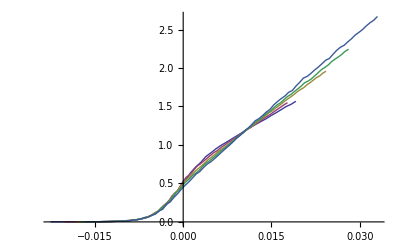

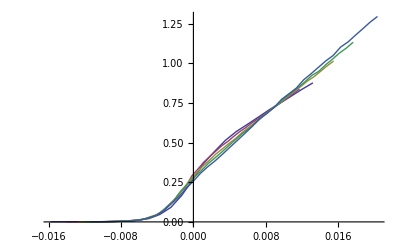

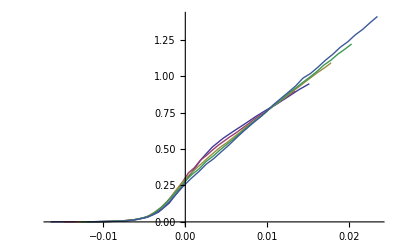

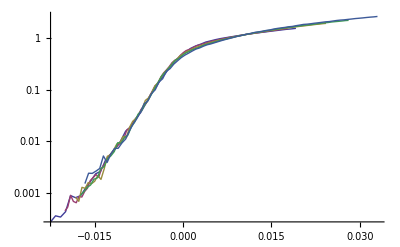

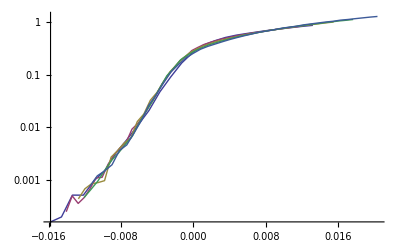

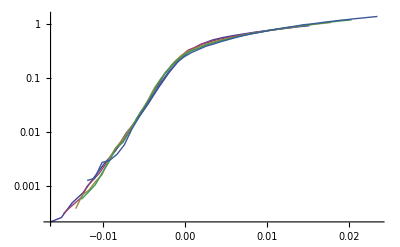

```mathematica
ListPlot[{input[5],input[10],input[20],input[30],input[50]},Joined->True]
ListPlot[{input1[5],input1[10],input1[20],input1[30],input1[50]},Joined->True]
ListPlot[{input2[5],input2[10],input2[20],input2[30],input2[50]},Joined->True]
ListLogPlot[{input[5],input[10],input[20],input[30],input[50]},Joined->True]
ListLogPlot[{input1[5],input1[10],input1[20],input1[30],input1[50]},Joined->True]
ListLogPlot[{input2[5],input2[10],input2[20],input2[30],input2[50]},Joined->True]
```

```mathematica
k0
c
ex
-a
zf
```

0.08122

0.194499

1.

0.325833

0.17

```mathematica
k0
c1
ex1
-a1
zf1
```

0.08122

0.123151

-0.402153

0.260812

0.13

```mathematica
k0
c2
ex2
-a2
zf2
```

0.08122

0.141019

-0.418901

0.266766

0.14

```mathematica
ClearAll[z,r,x,k]
r0=0;
For[ex=0,ex<1,ex+=0.005;


fit=LinearModelFit[pmaxdgdd[v],{1,x^-ex},x];
(*fit=NonlinearModelFit[Maxxs,model,{k,d},x,Weights->1/Errorx^2];*)

r=fit["RSquared"];

If[r>r0,
ffit=fit["BestFit"];
fitf=fit;
val=fit["ParameterTableEntries"];
r0=r;
ex4=ex;
]


]
ffit "fit : "
r0 "= r0"
ex4 "= ex4"
```

fit :  (0.0823851+4.18612/x^0.85)

0.997105 = r0

0.85 = ex4

```mathematica
ClearAll[z,r,x,k]
r0=0;
For[ex=0,ex<1,ex+=0.005;


fit=LinearModelFit[pmaxdg1dd[v],{1,x^-ex},x];
(*fit=NonlinearModelFit[Maxxs,model,{k,d},x,Weights->1/Errorx^2];*)

r=fit["RSquared"];

If[r>r0,
ffit=fit["BestFit"];
fitf=fit;
val1=fit["ParameterTableEntries"];
r0=r;
ex5=ex;
]


]
ffit "fit : "
r0 "= r0"
ex5"= ex5"
```

fit :  (0.0825797+3.82691/x^0.85)

0.983769 = r0

0.85 = ex5

```mathematica
ClearAll[z,r,x,k]
r0=0;
For[ex=0,ex<1,ex+=0.005;


fit=LinearModelFit[pmaxdg2dd[v],{1,x^-ex},x];
(*fit=NonlinearModelFit[Maxxs,model,{k,d},x,Weights->1/Errorx^2];*)

r=fit["RSquared"];

If[r>r0,
ffit=fit["BestFit"];
fitf=fit;
val2=fit["ParameterTableEntries"];
r0=r;
ex6=ex;
]


]
ffit "fit : "
r0 "= r0"
ex6"= ex6"
```

fit :  (0.0824612+3.18541/x^0.825)

0.991109 = r0

0.825 = ex6

```mathematica
pmaxdg1dd[v]
```

{{5000,0.0853},{10000,0.0842},{20000,0.0834},{30000,0.083},{50000,0.0831}}

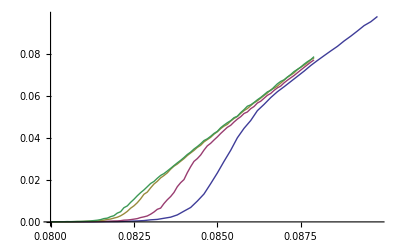

```mathematica
ListLinePlot[{g[v][5],g[v][10],g[v][30],g[v][50]}]
```

```mathematica
k4=val[[1]][[1]];
k5=val1[[1]][[1]];
k6=val2[[1]][[1]];

c4=val[[2]][[1]];
c5=val1[[2]][[1]];
c6=val2[[2]][[1]];
```

```mathematica
l1=5;
l2=10;
l3=20;
l4=50;
l5=30;
Do[

input4[l]=Table[{(g[v][l][[All,1]][[i]]-(k4+4*(l*1000)^(-ex4))),g[v][l][[All,2]][[i]]*(l*1000)^(-a)},{i,1,Length[g[v][l]]}];
input5[l]=Table[{(g1[v][l][[All,1]][[i]]-(k5+c5*(l*1000)^(-ex5))),g1[v][l][[All,2]][[i]]*(l*1000)^(-a1)},{i,1,Length[g1[v][l]]}];
input6[l]=Table[{(g2[v][l][[All,1]][[i]]-(k6+c6*(l*1000)^(-ex6))),g2[v][l][[All,2]][[i]]*(l*1000)^(-a2)},{i,1,Length[g2[v][l]]}];
,{l,{l1,l2,l3,l4,l5}}]
```

```mathematica
aux=1000;

For[z=0,z<0.4,z+=0.01,


Do[
dat[l]=Table[{(input4[l][[All,1]][[i]])*(l*1000)^z,input4[l][[All,2]][[i]]},{i,1,Length[input4[l]]}];
in[l]=Interpolation[dat[l]]
,{l,{l1,l2,l3,l4}}];


min=Max[dat[l1][[All,1]][[1]],dat[l2][[All,1]][[1]],dat[l3][[All,1]][[1]],dat[l4][[All,1]][[1]]];
max=Min[dat[l1][[All,1]][[Length[dat[l1]]]],dat[l2][[All,1]][[Length[dat[l2]]]],dat[l3][[All,1]][[Length[dat[l3]]]],dat[l4][[All,1]][[Length[dat[l4]]]]];

val=NIntegrate[Abs[Log[Max[in[l1][x],in[l2][x],in[l3][x],in[l4][x]]]-Log[Min[in[l1][x],in[l2][x],in[l3][x],in[l4][x]]]],{x,min,max}]/((max-min)*(Log[Max[in[l1][max],in[l2][max],in[l3][max],in[l4][max]]]-Log[Min[in[l1][min],in[l2][min],in[l3][min],in[l4][min]]]));
(*Print[val]*)
(*sum=Append[sum,{z,val}];*)

If[val<aux,
aux=val;
zf4=z;

]
]

aux
"= zf4"zf4
```

0.0434489

0.12 = zf4

```mathematica
aux=1000;

For[z=0,z<0.4,z+=0.01,


Do[
dat[l]=Table[{(input5[l][[All,1]][[i]])*(l*1000)^z,input5[l][[All,2]][[i]]},{i,1,Length[input5[l]]}];
in[l]=Interpolation[dat[l]]
,{l,{l1,l2,l3,l4}}];


min=Max[dat[l1][[All,1]][[1]],dat[l2][[All,1]][[1]],dat[l3][[All,1]][[1]],dat[l4][[All,1]][[1]]];
max=Min[dat[l1][[All,1]][[Length[dat[l1]]]],dat[l2][[All,1]][[Length[dat[l2]]]],dat[l3][[All,1]][[Length[dat[l3]]]],dat[l4][[All,1]][[Length[dat[l4]]]]];

val=NIntegrate[Abs[Log[Max[in[l1][x],in[l2][x],in[l3][x],in[l4][x]]]-Log[Min[in[l1][x],in[l2][x],in[l3][x],in[l4][x]]]],{x,min,max}]/((max-min)*(Log[Max[in[l1][max],in[l2][max],in[l3][max],in[l4][max]]]-Log[Min[in[l1][min],in[l2][min],in[l3][min],in[l4][min]]]));
(*Print[val]*)
(*sum=Append[sum,{z,val}];*)

If[val<aux,
aux=val;
zf5=z;

]
]

aux
"= zf5"zf5
```

0.0407562

0.11 = zf5

```mathematica
aux=1000;

For[z=0,z<0.4,z+=0.01,


Do[
dat[l]=Table[{(input6[l][[All,1]][[i]])*(l*1000)^z,input6[l][[All,2]][[i]]},{i,1,Length[input6[l]]}];
in[l]=Interpolation[dat[l]]
,{l,{l1,l2,l3,l4}}];


min=Max[dat[l1][[All,1]][[1]],dat[l2][[All,1]][[1]],dat[l3][[All,1]][[1]],dat[l4][[All,1]][[1]]];
max=Min[dat[l1][[All,1]][[Length[dat[l1]]]],dat[l2][[All,1]][[Length[dat[l2]]]],dat[l3][[All,1]][[Length[dat[l3]]]],dat[l4][[All,1]][[Length[dat[l4]]]]];

val=NIntegrate[Abs[Log[Max[in[l1][x],in[l2][x],in[l3][x],in[l4][x]]]-Log[Min[in[l1][x],in[l2][x],in[l3][x],in[l4][x]]]],{x,min,max}]/((max-min)*(Log[Max[in[l1][max],in[l2][max],in[l3][max],in[l4][max]]]-Log[Min[in[l1][min],in[l2][min],in[l3][min],in[l4][min]]]));
(*Print[val]*)
(*sum=Append[sum,{z,val}];*)

If[val<aux,
aux=val;
zf6=z;

]
]

aux
"= zf6"zf6
```

0.0389568

0.12 = zf6

```mathematica
l1=5;
l2=10;
l3=20;
l4=50;
l5=30;
Do[

input[l]=Table[{(g[v][l][[All,1]][[i]]-(k4+c4*(l*1000)^(-ex4)))*(l*1000)^(zf4),g[v][l][[All,2]][[i]]*(l*1000)^(-a)},{i,1,Length[g[v][l]]}];
input1[l]=Table[{(g1[v][l][[All,1]][[i]]-(k5+c5*(l*1000)^(-ex5)))*(l*1000)^(zf5),g1[v][l][[All,2]][[i]]*(l*1000)^(-a1)},{i,1,Length[g1[v][l]]}];
input2[l]=Table[{(g2[v][l][[All,1]][[i]]-(k6+c6*(l*1000)^(-ex6)))*(l*1000)^(zf6),g2[v][l][[All,2]][[i]]*(l*1000)^(-a2)},{i,1,Length[g2[v][l]]}];
,{l,{l1,l2,l3,l4,l5}}]
```

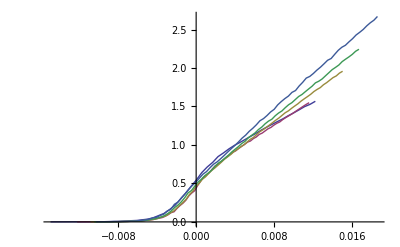

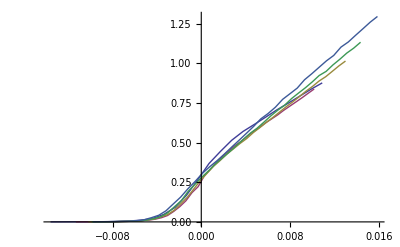

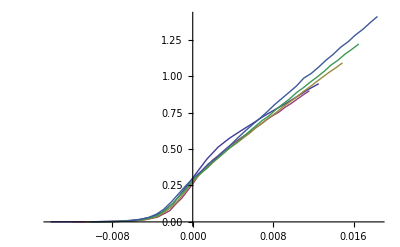

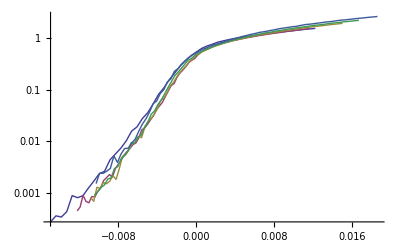

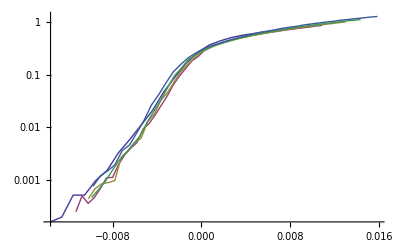

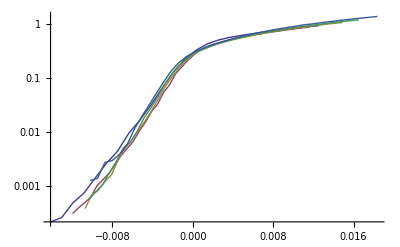

```mathematica
ListPlot[{input[5],input[10],input[20],input[30],input[50]},Joined->True]
ListPlot[{input1[5],input1[10],input1[20],input1[30],input1[50]},Joined->True]
ListPlot[{input2[5],input2[10],input2[20],input2[30],input2[50]},Joined->True]
ListLogPlot[{input[5],input[10],input[20],input[30],input[50]},Joined->True]
ListLogPlot[{input1[5],input1[10],input1[20],input1[30],input1[50]},Joined->True]
ListLogPlot[{input2[5],input2[10],input2[20],input2[30],input2[50]},Joined->True]
```

```mathematica
k0
c
ex
-a
zf
```

0.08122

0.194499

1.

0.325833

0.17

```mathematica
k0
c1
ex1
-a1
zf1
```

0.08122

0.123151

-0.402153

0.260812

0.13

```mathematica
k0
c2
ex2
-a2
zf2
```

0.08122

0.141019

-0.418901

0.266766

0.14

```mathematica
k4
c4
ex4
-a
zf4
```

0.0823851

4.18612

0.85

0.325833

0.12

```mathematica
k5
c5
ex5
-a1
zf5
```

0.0825797

3.82691

0.85

0.260812

0.11

```mathematica
k6
c6
ex6
-a2
zf6
```

0.0824612

3.18541

0.825

0.266766

0.12